# Some MPM Meshes

Remarks: Output requires node ID starting by 0!

```mathematica
OutputDirectory=ParentDirectory[NotebookDirectory[]]<>"/data/";
```

```mathematica
ParticleX2D[toelementmesh_]:=Module[
{MeshElements,MeshCoord,NoElements,PX,PV},
MeshCoord=toelementmesh["Coordinates"];
MeshElements=toelementmesh["MeshElements"]⟦1,1⟧;
NoElements=Length[MeshElements];
Return[Table[
(*Compute Particle Position PX (element center)*)
PX=Mean[MeshCoord⟦MeshElements⟦i⟧⟧];
(*Compute Particle Position PX (element center)*)
PV=Area[Polygon[MeshCoord⟦MeshElements⟦i⟧⟧]];
(*Output as 3d coordinates followed by volume*)
{PX⟦1⟧,PX⟦2⟧,0.0,PV}
,{i,NoElements}]]
]
```

#### Rectangular Q4-Grid

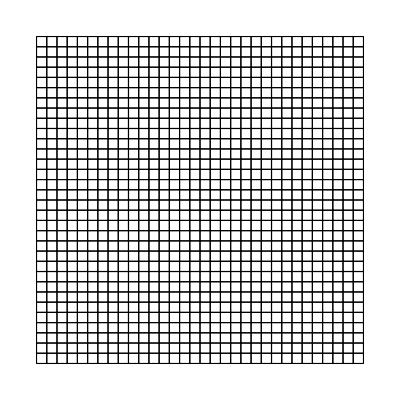

```mathematica
<<NDSolve`FEM`;
GridMesh=ToElementMesh[
Rectangle[{0,0},{1,1}]
,"MeshOrder"->1
,MaxCellMeasure->0.001
];
GridMesh["Wireframe"]
Node=GridMesh["Coordinates"];
ElementConnectivity=GridMesh["MeshElements"]⟦1,1⟧-1;
```

#### Falling Bar

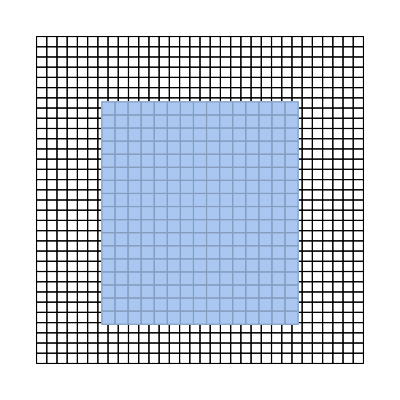

```mathematica
<<NDSolve`FEM`;
GridMesh=ToElementMesh[
Rectangle[{0,0},{1,1}]
,"MeshOrder"->1
,MaxCellMeasure->0.001
];
BarMesh=ToElementMesh[
Rectangle[{0.2,0.12},{0.8,0.8}]
,"MeshOrder"->1
,MaxCellMeasure->0.0018
];
Show[
GridMesh["Wireframe"],MeshRegion[BarMesh]]
```

```mathematica
Node=GridMesh["Coordinates"];
ElementConnectivity=GridMesh["MeshElements"]⟦1,1⟧-1;

Export[OutputDirectory<>"/falling_bar_node.txt",Node,"CSV"]
Export[OutputDirectory<>"/falling_bar_element.txt",ElementConnectivity,"CSV"]
```

/Users/sash/mpm_2d/data//falling_bar_node.txt

/Users/sash/mpm_2d/data//falling_bar_element.txt

```mathematica
Export[
OutputDirectory<>"/falling_bar_particle.txt",
ParticleX2D[BarMesh],
"CSV"]
```

/Users/sash/mpm_2d/data//falling_bar_particle.txt